# ListDensityPlot de 1/100∫_0^100 𝔼[Tr[𝒟^2(t)] ]dt

```mathematica
SetDirectory[NotebookDirectory[]];
```

## XXZ L=7,d=4,J_z=1,ω=0, barriendo ε y J_xy de 0 a 2 (paso = 0.1)

```mathematica
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/xxz_w_defect_L_7_Jz_1_d_4_omega_0.csv"]]
```

{{\varepsilon,J_{xy},promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

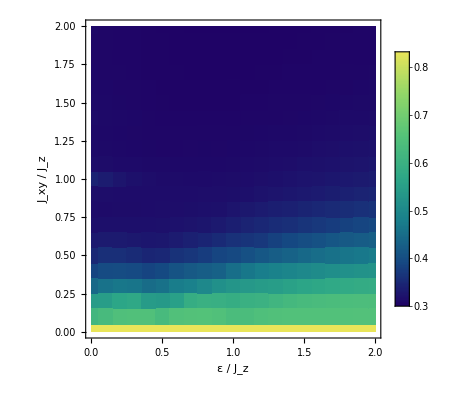

```mathematica
fontSize=22;

fig=ListDensityPlot[choiPurity,
ColorFunction->"BlueGreenYellow",
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"ε / J_z","J_xy / J_z"}
]
```

```mathematica
Export["tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_4.png",fig,"PNG"]
```

tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_4.png

## XXZ L=7,d=3,J_z=1,ω=0, barriendo ε y J_xy de 0 a 2 (paso = 0.1)

```mathematica
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/xxz_w_defect_L_7_Jz_1._d_3_omega_0..csv"]]
```

{{\varepsilon,J_{xy},promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

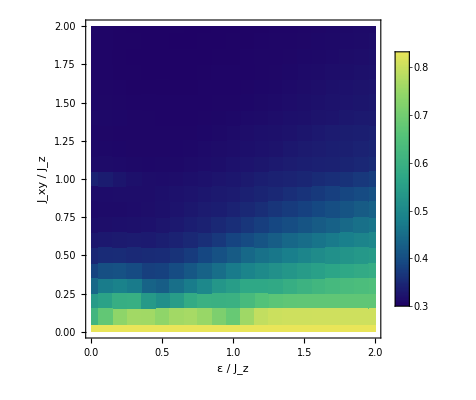

```mathematica
fontSize=22;

fig=ListDensityPlot[choiPurity,
ColorFunction->"BlueGreenYellow",
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"ε / J_z","J_xy / J_z"}
]
```

```mathematica
Export["tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_3.png",fig,"PNG"]
```

tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_3.png

## XXZ L=7,d=3,J_z=1,ω=0, barriendo ε y J_xy de 0 a 2 (paso = 0.1)

```mathematica
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/wisniacki_open_L_7_hx_1..csv"]]
```

{{hz,J,promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

```mathematica
choiPurity=Flatten[Table[{Subdivide[0.,2.,20][[i]],Subdivide[0.,2.,20][[j]],choiPurity[[21*(i-1)+j,3]]},{i,21},{j,21}],1];
```

```mathematica
Select[Round[choiPurity,10.^-2],#[[1]]==2.00&&#[[2]]==0.0&]
```

{{2.,0.,1.}}

```mathematica
Select[Round[choiPurity,10.^-2],#[[3]]>=0.7&]
```

{{0.,0.,1.},{0.1,0.,1.},{0.2,0.,1.},{0.3,0.,1.},{0.4,0.,1.},{0.5,0.,1.},{0.6,0.,1.},{0.7,0.,1.},{0.8,0.,1.},{0.9,0.,1.},{1.,0.,1.},{1.1,0.,1.},{1.2,0.,1.},{1.3,0.,1.},{1.4,0.,1.},{1.5,0.,1.},{1.6,0.,1.},{1.7,0.,1.},{1.8,0.,1.},{1.9,0.,1.},{2.,0.,1.},{2.,0.1,0.7}}

```mathematica
{Min[choiPurity[[;;,3]]],Select[Round[choiPurity,10.^-2],#[[3]]==0.28&]}
```

{0.277784,{{0.2,0.9,0.28},{0.2,1.,0.28},{0.2,1.1,0.28},{0.2,1.2,0.28},{0.2,1.3,0.28},{0.3,0.8,0.28},{0.3,0.9,0.28},{0.3,1.,0.28},{0.3,1.1,0.28},{0.3,1.2,0.28},{0.3,1.3,0.28},{0.3,1.4,0.28},{0.4,0.8,0.28},{0.4,0.9,0.28},{0.4,1.,0.28},{0.4,1.1,0.28},{0.4,1.2,0.28},{0.4,1.3,0.28},{0.4,1.4,0.28},{0.5,0.8,0.28},{0.5,0.9,0.28},{0.5,1.,0.28},{0.5,1.1,0.28},{0.5,1.2,0.28},{0.5,1.3,0.28},{0.5,1.4,0.28},{0.5,1.5,0.28},{0.6,0.8,0.28},{0.6,0.9,0.28},{0.6,1.,0.28},{0.6,1.1,0.28},{0.6,1.2,0.28},{0.6,1.3,0.28},{0.6,1.4,0.28},{0.6,1.5,0.28},{0.7,1.,0.28},{0.7,1.1,0.28},{0.7,1.2,0.28},{0.7,1.3,0.28}}}

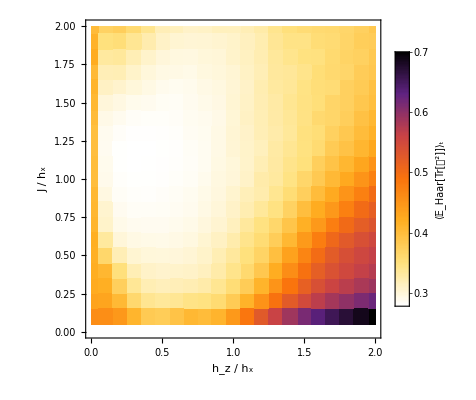

```mathematica
fontSize=22;

fig=ListDensityPlot[choiPurity,
ColorFunction->(ColorData["SunsetColors"][1-#]&),ColorFunctionScaling->True,
PlotRange->{0.25,0.75},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"}
]
```

```mathematica
Export["tmp/temporal_avg_haar_avg_choi_purity_wisniacki_open_L_7_hx_1.png",fig,"PNG"]
```

tmp/temporal_avg_haar_avg_choi_purity_wisniacki_open_L_7_hx_1.png